```mathematica
1/Integrate[Exp[-x^2/2],{x,-5,5}]//N
```

0.398943

```mathematica
Exp[-5^2/2]//N
```

3.72665×10^-6

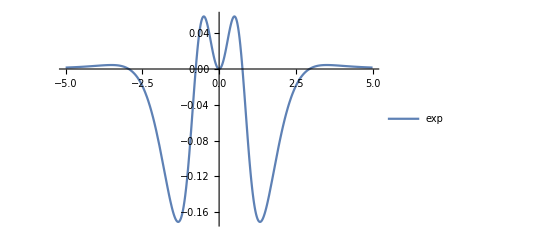

```mathematica
Plot[{-Exp[-x^2/2]+1/(1+x^4)},{x,-5,5},PlotLegends->{"exp","lorentz"}]
```

```mathematica
Minimize[-Exp[-x^2/2]+2.4/(1+x^4),{x}∈Interval[{-5,5}]]//N
```

{0.00383014,{x→5.}}

```mathematica
Clear[F];
F[x_]=Integrate[1/(1+x^4),x]
```

1/(4 √2)(-2 ArcTan[1-√2 x]+2 ArcTan[1+√2 x]-Log[1-√2 x+x^2]+Log[1+√2 x+x^2])

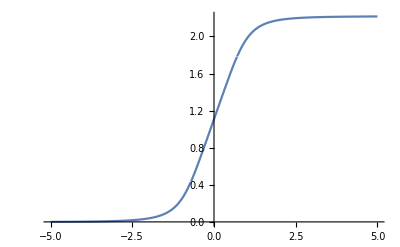

```mathematica
Plot[F[x]-F[-5],{x,-5,5}]
```

```mathematica
F/.x->5//N
```

1.10806

```mathematica
data=Import["data.csv"]
```

Import::nffil: File not found during Import.

$Failed